## Functions Location

```mathematica
SetDirectory[NotebookDirectory[]];
paths=FileNames["*nls",ParentDirectory[Directory[]]<>"/Simulation"];
fileNames=(FileNameSplit[#]&/@paths)//Transpose//Last;
raw=Import[#,"Table"]&/@paths;
functions=Cases[#,({"to-report",a_,__}|{"to-report",a_}|{"to",a_}|{"to",a_,__}|{"to ",a_,__})->a]&/@raw;
Grid[Prepend[{fileNames,Grid[{#}//Transpose]&/@functions}//Transpose,{"FileName","Functions"}],Frame->All,Background->{None,{LightBlue}}]
Export["functionsLocation.png",%,ImageSize->2000,ImageResolution->100]
```

FileName | Functions
auxiliaryFunctions.nls | random-bool
random-integer-between
transition-age-variation
movement-speed-variation
setRandomXY
convert_ratio_days_to_ticks
convert_days_to_ticks
toggle_weekend
toggle_day_night
update_days_number
update_temperature
update_contacts_bools
update-warmup
update_max_eggs
update_egg_inhibition_probability
update_metabolic_rate
controlMeasures.nls | breeding-site-extermination
kill-breeding-site
fumigate
replace-breeding-site
breeding-site-replacement
update-fogging-parameters
fogging-refill
global.nls | set-global-variables
set-initial-population
extermination-probability
larva-mortality-probability
pupa-mortality-probability
update-larva-density-death-probability
larva-density-death-probability
temperature-climate-model
temperature-avg-climate-model
larva-density-egg-hatching-inhibition
fogging-process
go.nls | go
act-aedesp
act-humanp
act-breedingZonesp
act-sugarsp
release-mosquitoesControl
GoogleMap_HET.nls | set-coordinates
GoogleMap_HOM.nls | set-coordinates
humanBehaviour.nls | act-human-day
act-human-worker
act-human-non-worker
act-human-night
kill-mosquito-probabilistically
sickness-goHome-rest
exterminate-and-or-replace
contact-human
human-contact-human
contact-house
human-contact-house
human-contact-workZone
die-human
mosquitoBehaviour.nls | act-mosquito-day
act-mosquito-night
act-hungry
act-feed
act-resetFemale
act-dead
act-egg
act-larva
act-pupa
act-adult
act-adult-night
probabilistic-natural-death
probabilistic-die-by-starvation
probabilistic-die-by-predation
movement.nls | move-pseudo-random-walking
move-probabilistically-towards
wander-around-house
wander-towards-house
randomScenarios.nls | set-coordinates1
set-coordinates2
set-coordinates3
set-coordinates4
set-coordinates5
release.nls | release-control
release-control-mosquitos
release-control-mosquitos-program
release-sterile
release-oxitec
release-fitness
release-wolbachia
release-neutral
reproductionRoutines.nls | act-mate
mate-as-female
mate-as-male
act-layEggs
reproduce-sterile
reproduce-wolbachia
reproduce-ridl
reproduce-fitness
reproduce-normal
act-bloodfeed
act-reproductive
act-not-bloodfed-yet
act-bloodfed-yet
schoolfield.nls | evaluate-schoolfield-model-ratio
evaluate-schoolfield-constants
set-batch-evaluate-schoolfield-constants
evaluate-schoolfield-model-ratio-with-constants
evaluate-schoolfield-model-days-with-constants
calculate_phases_transitions_time_in_current_tick
calculate_phases_transitions_ratio
transitionsCreation.nls | create_transition_ages
create_transition_ages_wolbachia
create_movement_speeds
turtlesCreation.nls | reproduce_RIDL
reproduce
setup
create-humans-houses-breeding-landmarks
setup-terrain
create-ovitraps-population
create-ovitrap-around-coordinates
create-workZones-population
create-sugars-population
create-sugarBaits-population
create-population
create-house-at-coordinates
create-landmark-and-breeding-zone-around-coordinates
create-humans-at-houses
xmlExport.nls | XML-write-parameters
XML-write-tick-outputs
XML-write-tail-outputs
Append_Final_Bites_Lists
XML-setup-name
XML-init-write
XML-write-header
XML-write-entry
XML-write-simple-entry
XML-finish-write
XML-init-write-ticks-body
XML-finish-write-ticks-body
XML-init-write-tail-body
XML-finish-write-tail-body

functionsLocation.png

## Functions Tree

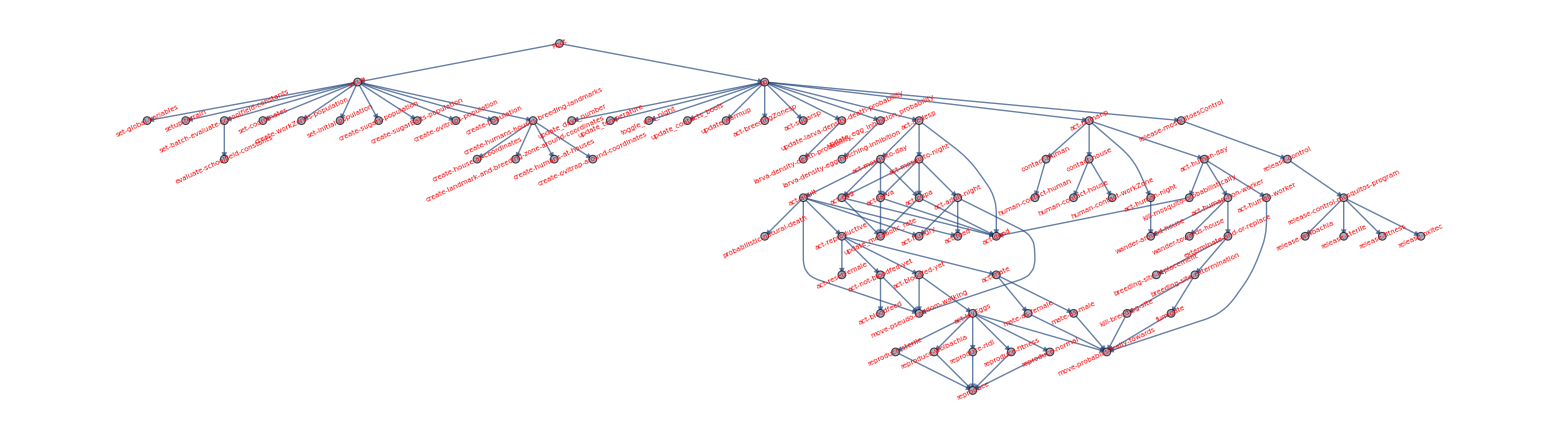

functionsTree.eps

functionsTree.png

```mathematica
SetDirectory[NotebookDirectory[]];
panelLabel[lbl_]:=Panel[lbl,FrameMargins->0,Background->Lighter[Yellow,0.7]]
data=Map[StringTrim,Import["FunctionsTreeIN.csv"],Infinity];
tree=Flatten[((#[[1]]->#[[2]])&/@(Partition[#,2,1]))&/@data];
Graph[tree//DeleteDuplicates,ImageSize->1750,VertexSize->.2,VertexLabels->(Placed["Name",Center,Rotate[#,25Degree]&]),VertexLabelStyle->(Directive[Red,7]),GraphLayout->"LayeredDigraphEmbedding",EdgeShapeFunction->GraphElementData["ShortFilledArrow","ArrowSize"->0.005]]
Export["functionsTree.eps",%,ImageSize->2000,ImageResolution->200]
Export["functionsTree.png",%%,ImageSize->5000,ImageResolution->200]
```

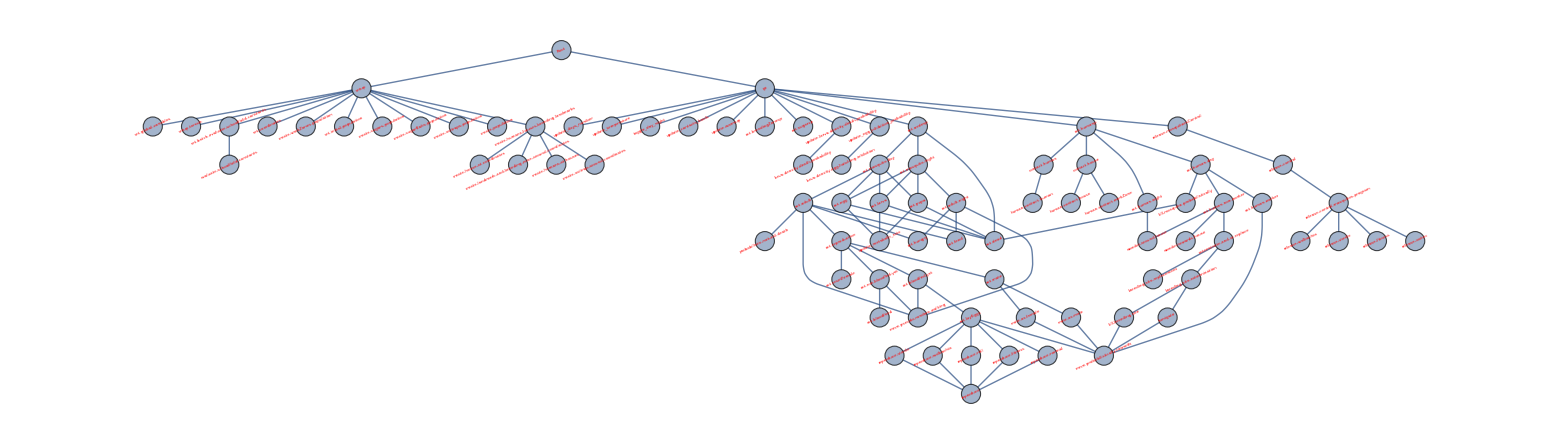

functionsTree.eps

functionsTree.png

```mathematica
SetDirectory[NotebookDirectory[]];
panelLabel[lbl_]:=Rotate[Panel[Style[lbl,5],FrameMargins->0,Background->Lighter[Blue,.9]],25Degree]
data=Map[StringTrim,Import["FunctionsTreeIN.csv"],Infinity];
tree=Flatten[((#[[1]]->#[[2]])&/@(Partition[#,2,1]))&/@data];
Graph[tree//DeleteDuplicates,ImageSize->1750,VertexSize->.5,VertexLabels->(Placed["Name",Center,panelLabel]),VertexLabelStyle->(Directive[Red,2]),GraphLayout->"LayeredDigraphEmbedding",EdgeShapeFunction->GraphElementData["ShortFilledArrow","ArrowSize"->0.005]]
Export["functionsTree.eps",%,ImageSize->2000,ImageResolution->200]
Export["functionsTree.png",%%,ImageSize->5000,ImageResolution->200]
```